# Interpolation

## Algoritmo de Vandermonde

```mathematica
p[x_]:=a+b x+c x^2
```

```mathematica
sol=Solve[{p[x1]==y1,p[x2]==y2,p[x3]==y3},{a,b,c}]
```

{{a→-(-x2^2 x3 y1+x2 x3^2 y1+x1^2 x3 y2-x1 x3^2 y2-x1^2 x2 y3+x1 x2^2 y3)/((-x1+x2) (x2-x3) (-x1+x3)),b→-(x2^2 y1-x3^2 y1-x1^2 y2+x3^2 y2+x1^2 y3-x2^2 y3)/((x1-x2) (x1-x3) (x2-x3)),c→-(-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)/((x1-x2) (x1-x3) (x2-x3))}}

```mathematica
p2=p[x]/.sol[[1]]
```

-(x^2 (-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3))/((x1-x2) (x1-x3) (x2-x3))-(x (x2^2 y1-x3^2 y1-x1^2 y2+x3^2 y2+x1^2 y3-x2^2 y3))/((x1-x2) (x1-x3) (x2-x3))-(-x2^2 x3 y1+x2 x3^2 y1+x1^2 x3 y2-x1 x3^2 y2-x1^2 x2 y3+x1 x2^2 y3)/((-x1+x2) (x2-x3) (-x1+x3))

```mathematica
p2/.x->{x1,x2,x3}//Simplify
```

{y1,y2,y3}

## InterpolatingPolynomial

### Example 1

```mathematica
InterpolatingPolynomial[{{x1,y1},{x2,y2},{x3,y3}},x]
```

y1+(x-x1) ((-y1+y2)/(-x1+x2)+((x-x2) (-(-y1+y2)/(-x1+x2)+(-y2+y3)/(-x2+x3)))/(-x1+x3))

```mathematica
%/.x->{x1,x2,x3}//Simplify
```

{y1,y2,y3}

### Ejemplo 2

```mathematica
f[x_]:=Erf[x]
```

```mathematica
min=0.;
max=4.;
```

```mathematica
data=Array[{#,f[#]}&,21,{min,max}]
```

{{0.,0.},{0.2,0.222703},{0.4,0.428392},{0.6,0.603856},{0.8,0.742101},{1.,0.842701},{1.2,0.910314},{1.4,0.952285},{1.6,0.976348},{1.8,0.989091},{2.,0.995322},{2.2,0.998137},{2.4,0.999311},{2.6,0.999764},{2.8,0.999925},{3.,0.999978},{3.2,0.999994},{3.4,0.999998},{3.6,1.},{3.8,1.},{4.,1.}}

```mathematica
poly[x_]:=InterpolatingPolynomial[data,x]
```

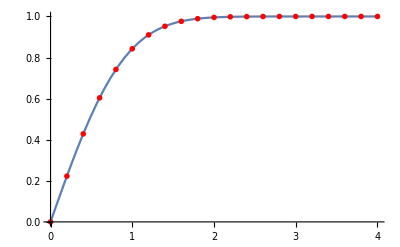

```mathematica
Plot[poly[x],{x,min,max},PlotRange->All,
Epilog->{Red,PointSize[0.01],Point[data]}]
```

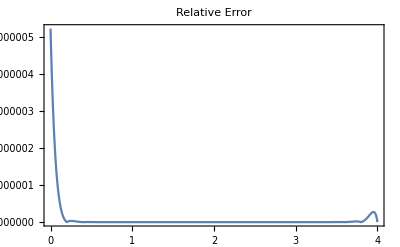

```mathematica
Plot[Abs[f[x]-poly[x]]/Abs[f[x]],{x,min,max},
PlotLabel->"Relative Error",Frame->True,PlotRange->All]
```

### Ejemplo 3

```mathematica
g[x_]:=1/(1+25 x^2)
```

```mathematica
min=-1.;
max=1.;
```

```mathematica
data=Array[{#,g[#]}&,21,{min,max}]
```

{{-1.,0.0384615},{-0.9,0.0470588},{-0.8,0.0588235},{-0.7,0.0754717},{-0.6,0.1},{-0.5,0.137931},{-0.4,0.2},{-0.3,0.307692},{-0.2,0.5},{-0.1,0.8},{0.,1.},{0.1,0.8},{0.2,0.5},{0.3,0.307692},{0.4,0.2},{0.5,0.137931},{0.6,0.1},{0.7,0.0754717},{0.8,0.0588235},{0.9,0.0470588},{1.,0.0384615}}

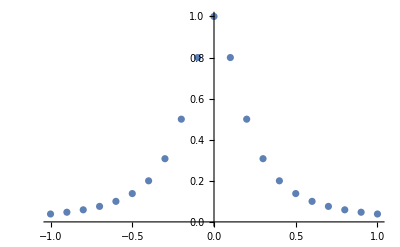

```mathematica
ListPlot[data]
```

```mathematica
poly[x_]=InterpolatingPolynomial[data,x]
```

0.0384615+(1.+x) (0.+(-1.+x) (-0.961538+(0.+x) (-1.44231+(0.6+x) (2.08636+(-0.7+x) (-4.26343+(-0.4+x) (-4.96243+(0.9+x) (5.01579+(-0.9+x) (15.0228+(0.3+x) (16.9253+(0.8+x) (-60.8443+(-0.2+x) (64.5867+(-0.8+x) (142.994+(0.5+x) (-197.215+(-0.6+x) (-307.011+(0.7+x) (-967.865+(0.1+x) (2393.64+(-0.5+x) (3642.5+(0.4+x) (-15610.7+(-0.3+x) (-26017.9+260179. (0.2+x))))))))))))))))))))

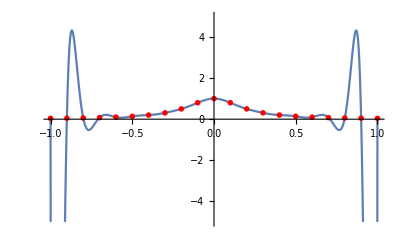

```mathematica
Plot[poly[x],{x,min,max},PlotRange->{-5,5},Epilog->{Red,PointSize[0.01],Point[data]}]
```

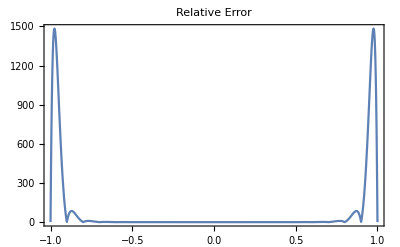

```mathematica
Plot[Abs[g[x]-poly[x]]/Abs[g[x]],{x,min,max},PlotLabel->"Relative Error",Frame->True,PlotRange->All]
```

Si el error relativo es menor a 10^-6 para todo punto en el dominio entonces tiene 6 digitos significativos.

## Splines

### Example 1

```mathematica
runge[x_]:=1/(1+25 x^2)
```

```mathematica
data=Array[{#,runge[#]}&,100,{min,max}];
```

```mathematica
spl=Interpolation[data,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
spl[3.04]
```

-0.93577

```mathematica
spl[{0.,3.1}]
```

{0.999993,-1.02859}

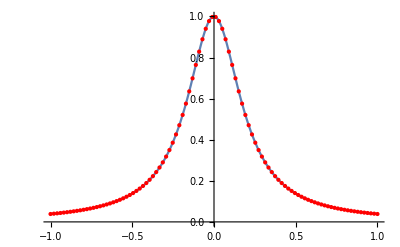

```mathematica
Plot[spl[x],{x,-1,1},Epilog->{Red,Point[data]}]
```

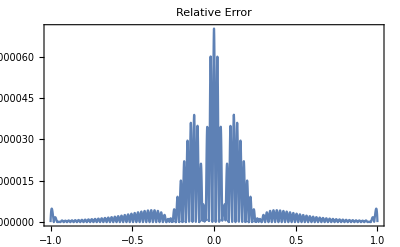

```mathematica
Plot[Abs[runge[x]-spl[x]]/Abs[runge[x]],{x,-1,1},PlotLabel->"Relative Error",Frame->True,PlotRange->All]
```

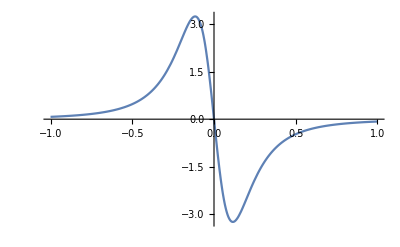

```mathematica
Plot[spl'[x],{x,-1,1}]
```

```mathematica
FindRoot[spl''[x],{x,0.1}]
```

{x→0.115481}

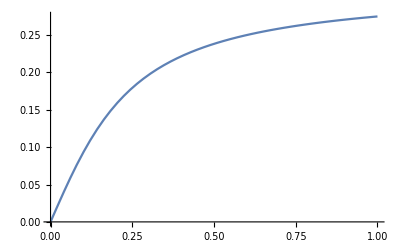

```mathematica
Plot[NIntegrate[spl[y],{y,0,x}],{x,0,1}]
```

### Example 2

```mathematica
circle[x_]:=√(1-x^2)
```

```mathematica
data=Array[{#,circle[#]}&,80,{-1.,1.}];
```

```mathematica
spl=Interpolation[data,Method->"Spline"]
```

InterpolatingFunction[…]

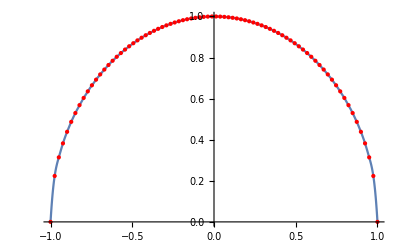

```mathematica
Plot[spl[x],{x,-1,1},Epilog->{Red,Point[data]}]
```

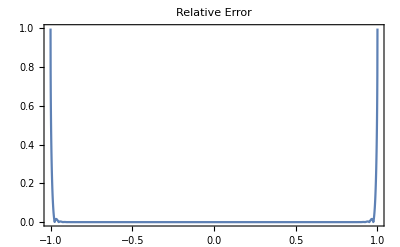

```mathematica
Plot[Abs[circle[x]-spl[x]]/Abs[circle[x]],{x,-1,1},PlotLabel->"Relative Error",Frame->True,PlotRange->All]
```

### Lagrange Interpolation

```mathematica
data=Array[{#,runge[#]}&,30,{min,max}];
```

```mathematica
spl=Interpolation[data,Method->"Lagrange"]
```

InterpolatingFunction[…]

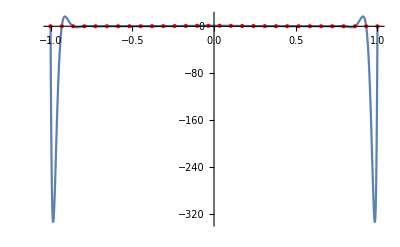

```mathematica
Plot[spl[x],{x,-1,1},Epilog->{Red,Point[data]},PlotRange->All]
```

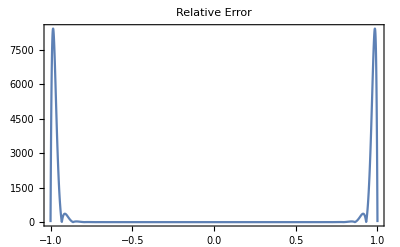

```mathematica
Plot[Abs[runge[x]-spl[x]]/Abs[runge[x]],{x,-1,1},PlotLabel->"Relative Error",Frame->True,PlotRange->All]
```

# Pregunta 5

## Interpolación de puntos de la tierra

```mathematica
crustData=Import["Data/crust.dat"];
innerCoreData=Import["Data/innerCore.dat"];
lowerMantleData=Import["Data/lowerMantle.dat"];
outerCoreData=Import["Data/outerCore.dat"];
upperMantleData=Import["Data/upperMantle.dat"];
```

```mathematica
CalculateMass[data_,interpMethod_]:=
Module[{minX,maxX,interp,distanceData},
distanceData=MapAt[Quantity[#,"Kilometers"]&,data,{All,1}](*We apply the units of km to the distances*);
distanceData=MapAt[Quantity[#,"Grams"/"Centimeters"^3]&,distanceData,{All,2}](*We apply the units of km to the distances*);
distanceData=MapAt[UnitConvert[#,"Kilograms"/"Kilometers"^3]&,distanceData,{All,2}];(*Change units to Kg/Km^3*)
distanceData=QuantityMagnitude[distanceData];

minX=distanceData[[1]][[1]];
maxX=distanceData[[-1]][[1]];
interp=Interpolation[distanceData,Method->interpMethod];
Quantity[NIntegrate[interp[x]*4π x^2,{x,minX,maxX}],"Kilograms"]
]
```

```mathematica
fullData={crustData,upperMantleData,lowerMantleData,outerCoreData,innerCoreData};
```

```mathematica
interpMethods={"Lagrange","Spline","Spline","Spline","Lagrange"};
```

```mathematica
merge=Partition[Riffle[fullData,interpMethods],2];
```

```mathematica
interpolations=Table[Interpolation[dat[[1]],Method->dat[[2]]],{dat,merge}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
plots=Table[Plot[interpolations[[i]][x],{x,fullData[[i]][[1]][[1]],fullData[[i]][[-1]][[1]]},PlotRange->All,
Epilog->{Red,PointSize[0.01],Point[fullData[[i]]]},ImageSize->Large],{i,Length[fullData]}];
```

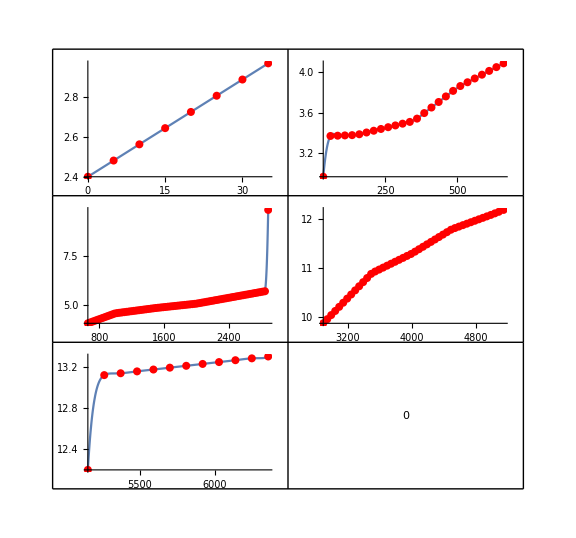

```mathematica
GraphicsGrid[ArrayReshape[plots,{3,2}],Frame->All,ImageSize->Large]
```

```mathematica
masses=Inner[CalculateMass[#1,#2]&,fullData,interpMethods,List]
```

{5.07239×10^17 kg,4.60477×10^21 kg,5.31991×10^23 kg,5.40028×10^24 kg,6.66562×10^24 kg}

```mathematica
Total[masses]
```

1.26025×10^25 kg